```mathematica
rho[x_,z_]:=0.5(1+Erf[(z-z0)*yv+pert*Cos[x]])(ph-pl)+pl;
pl=0.1111;ph=1;pert=0.5;z0=2.4;yv=4096/(1.5*32);
```

```mathematica
p[x_,z_]=∫(0.5(1+Erf[(z-z0)*yv+pert*Cos[x]])(ph-pl)+pl)ⅆz
```

-1.33332+0.00293852 2.71828^(-7281.78 (2.4-1. z-0.00585938 Cos[x])^2)+0.55555 z+0.00325518 Cos[x]+(1.06668-0.44445 z-0.0026042 Cos[x]) Erf[204.8-85.3333 z-0.5 Cos[x]]

```mathematica
FullSimplify[%1]
```

ⅇ^(-0.25 Cos[x]^2) (6.87547989134567×10^-18219 ⅇ^((34952.5-7281.78 z) z+(204.8-85.3333 z) Cos[x])+0.55555 ⅇ^(0.25 Cos[x]^2) z+(-0.44445 ⅇ^(0.25 Cos[x]^2) z+ⅇ^(0.125 Cos[2. x]) (1.20871-0.00295094 Cos[x])) Erf[204.8-85.3333 z-0.5 Cos[x]])

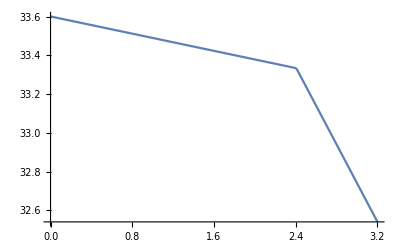

-Graphics-

```mathematica
Plot[35-p[Pi,z]-1.666111165500574,{z,0,4*z0/3}]
```

```mathematica
35-p[Pi,2.4]-33.3335
```

1.66611

```mathematica
35-p[Pi,2.4]-1.666111165500574
```

33.3335

```mathematica
35-p[Pi,0]-1.666111165500574
```

33.6012

```mathematica
1/yv ⅇ^(yv^2 (-1. z^2-1. z0^2)-1. pert^2 Cos[x]^2) (ⅇ^(yv (2. yv z z0+pert (-2. z+2. z0) Cos[x])) (0.28209479177387814 ph-0.28209479177387814 pl)+ⅇ^(yv^2 (1. z^2+1. z0^2)+1. pert^2 Cos[x]^2) (0.5 ph+0.5 pl) yv z+ⅇ^(yv^2 (1. z^2+1. z0^2)) (ⅇ^(1. pert^2 Cos[x]^2) (0.5 ph-0.5 pl) yv z+ⅇ^(pert^2 (0.5+0.5 Cos[2. x])) ((-0.5 ph+0.5 pl) yv z0+pert (0.5 ph-0.5 pl) Cos[x])) Erf[yv z-1. yv z0+pert Cos[x]])
```

0.0117188 ⅇ^(7281.78 (-5.76-1. z^2)-0.25 Cos[x]^2) (0.250754 ⅇ^(85.3333 (409.6 z+0.5 (4.8-2. z) Cos[x]))+47.4069 ⅇ^(7281.78 (5.76+1. z^2)+0.25 Cos[x]^2) z-ⅇ^(7281.78 (5.76+1. z^2)) (37.9264 ⅇ^(0.25 Cos[x]^2) z+ⅇ^(0.25 (0.5+0.5 Cos[2. x])) (-91.0234+0.222225 Cos[x])) Erf[204.8-85.3333 z-0.5 Cos[x]])